```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Common functions

### Modular

```mathematica
Δ1[q_]:=DedekindEta[1/(2π ⅈ)Log[q]]^24
Δ2[q_]:=DedekindEta[1/(π ⅈ)Log[q]]^24
polar[w_] := CoefficientList[q^(-(2 w)/24) DeleteCases[Assuming[q>0,Series[Δ1[q]^((2 w)/24),{q,0,0}]]//Normal, _Integer], q]
```

### Mock modular

```mathematica
E2[q_] := 1-24Sum[(n q^n)/(1-q^n) ,{n,1,500}]
```

```mathematica
kfnc[w_,x_,y_,c_]:=ⅈ^-w Total[ Flatten[ Table[ If[GCD[c,d]==1 && Mod[(a*d-1),c]==0,Exp[2π ⅈ(a/c y+d/c x)],0] ,{d,-c,-1},{a,0,c-1} ] ] ]
```

mp1 is the analog I_11 in C.8 of 2112.10023. mp2 is the analog of I_12.

```mathematica
m0[n_,n1_ , w_] := 24/w n Abs @ Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)N[BesselI[1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]], {c,1,10}]
```

```mathematica
m0l[n_,n1_ , w_] := 24/w n Abs @ Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)N[BesselI[1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]], n->0 ], {c,1,10}]
```

```mathematica
mp1[n_,n1_ , w_] := 24/w n Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)(N[BesselI[-1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), {c,1,10}]
```

```mathematica
mp2[n_,n1_ , w_] := 24/w n Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)( (2w c)/(4 π √(n  Abs[n1-(-(2w)/24)]))N[BesselI[-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), {c,1,10}]
```

```mathematica
mp1l[n_,n1_ , w_] := 24/w n Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)(N[BesselI[-1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), n->0 ], {c,1,10}]
```

```mathematica
mp2l[n_,n1_ , w_] := 24/w n Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)( (2w c)/(4 π √(n  Abs[n1-(-(2w)/24)]))N[BesselI[-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), n->0 ], {c,1,10}]
```

```mathematica
mp1re[n_,n1_ , w_] :=Re[mp1[n,n1,w]]
mp1abs[n_,n1_ , w_] :=Abs[mp1[n,n1,w]]
mp2re[n_,n1_ , w_] :=Re[mp2[n,n1,w]]
mp2abs[n_,n1_ , w_] :=Abs[mp2[n,n1,w]]
```

```mathematica
mp1lre[n_,n1_ , w_] :=Re[mp1l[n,n1,w]]
mp1labs[n_,n1_ , w_] :=Abs[mp1l[n,n1,w]]
mp2lre[n_,n1_ , w_] :=Re[mp2l[n,n1,w]]
mp2labs[n_,n1_ , w_] :=Abs[mp2l[n,n1,w]]
```

```mathematica
cn0[n_, n1_, w_] := If[n==0,  m0l[n,n1,w],m0[n,n1,w]]  (* Or you can directly put 0 for n=0*)
```

```mathematica
cn1[n_, n1_, w_] := If[n==0,  mp1l[n,n1,w],mp1[n,n1,w]]
cn1re[n_, n1_, w_] := If[n==0,  mp1lre[n,n1,w],mp1re[n,n1,w]]
cn1abs[n_, n1_, w_] := If[n==0,  mp1labs[n,n1,w],mp1abs[n,n1,w]]
```

```mathematica
cn2[n_, n1_, w_] := If[n==0,  mp2l[n,n1,w],mp2[n,n1,w]]
cn2re[n_, n1_, w_] := If[n==0,  mp2lre[n,n1,w],mp2re[n,n1,w]]
cn2abs[n_, n1_, w_] := If[n==0,  mp2labs[n,n1,w],mp2abs[n,n1,w]]
```

```mathematica
ψ0[n_, w_] := Total[Table[ polar[w][[i]] cn0[n, i-1,w], {i,Length[polar[w]]}] ]
```

```mathematica
ψ1[n_, w_] := Total[Table[ polar[w][[i]] cn1[n, i-1,w], {i,Length[polar[w]]}] ]
ψ1re[n_, w_] := Total[Table[ polar[w][[i]] cn1re[n, i-1,w], {i,Length[polar[w]]}] ]
ψ1abs[n_, w_] := Total[Table[ polar[w][[i]] cn1abs[n, i-1,w], {i,Length[polar[w]]}] ]
```

```mathematica
ψ2[n_, w_] := Total[Table[ polar[w][[i]] cn2[n, i-1,w], {i,Length[polar[w]]}] ]
ψ2re[n_, w_] := Total[Table[ polar[w][[i]] cn2re[n, i-1,w], {i,Length[polar[w]]}] ]
ψ2abs[n_, w_] := Total[Table[ polar[w][[i]] cn2abs[n, i-1,w], {i,Length[polar[w]]}] ]
```

### Jacobi

```mathematica
datadefn[rawData_,minLen_]:=Module[{newkeysTemp,newKeys,newVals,data},
newkeysTemp = If[Length[#]>= minLen, #, ##&[] ] & /@ Keys[rawData];
newKeys =newkeysTemp[[All,;;minLen]];
newVals = If[Length[Keys[#]]>= minLen, Values[#], ##&[] ] & /@ rawData;
data = Thread[newKeys ->newVals];
Return[data]
]
```

```mathematica
allprodθ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt = Thread[cq -> wt];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
theta1[k_,nq_,nu_]:=allprodθ[1,k,2, 0, 3, 0, 4, 0, nq, nu]
theta2[l_,nq_,nu_]:=allprodθ[1,0,2, l, 3, 0, 4, 0, nq, nu]
theta3[m_,nq_,nu_]:=allprodθ[1,0,2, 0, 3, m, 4, 0, nq, nu]
theta4[n_,nq_,nu_]:=allprodθ[1,0,2, 0, 3, 0, 4, n, nq, nu]
```

```mathematica
allprodθbyΔ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}]];
th2  = If[k<0, u^-k th1 ,th1 ];
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
allprodθbyΔu0[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[ EllipticTheta[t2,0,q]^l EllipticTheta[t3,0,q]^m EllipticTheta[t4,0,q]^n,{q,0,nq}]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th1,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
theta1byΔ[k_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,k,2, 0, 3, 0, 4, 0, nq, nu,qInPower]
theta2byΔ[l_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, l, 3, 0, 4, 0, nq, nu,qInPower]
theta3byΔ[m_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, 0, 3, m, 4, 0, nq, nu,qInPower]
theta4byΔ[n_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, 0, 3, 0, 4, n, nq, nu,qInPower]
```

```mathematica
theta1byΔu0[k_, nq_, qInPower_] := allprodθbyΔ[1,k, 2, 0, 3, 0, 4, 0, nq, 0,qInPower]
theta2byΔu0[l_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, l, 3, 0, 4, 0, nq, 0,qInPower]
theta3byΔu0[m_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, 0, 3, m, 4, 0, nq, 0,qInPower]
theta4byΔu0[n_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, 0, 3, 0, 4, n, nq, 0,qInPower]
```

```mathematica
allprodθwrite[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt =Join[cq[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq]];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
allprodθbyΔwrite[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_, qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq,cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
(*cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);*)
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
(*dt =Join[cq[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq]];*)
dt =Join[cq2[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq2]];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
klmnpos[rng_,n_]:= Values[FindInstance[{-rng<a<rng, -rng<b<rng, -rng<c<rng, -rng<d<rng, a+b+c+d>0},{a,b,c,d},Integers, n]];
klmnposonly[rng_,n_]:= Values[FindInstance[{0<a<rng, 0<b<rng, 0<c<rng,0<d<rng, a+b+c+d>0},{a,b,c,d},Integers, n]];
klmnneg[rng_,n_]:= Values[FindInstance[{-rng<a<rng, -rng<b<rng, -rng<c<rng, -rng<d<rng, a+b+c+d<0},{a,b,c,d},Integers, n]];
klmnnegonly[rng_,n_]:= Values[FindInstance[{-rng<a<0, -rng<b<0, -rng<c<0, -rng<d<0, a+b+c+d<0},{a,b,c,d},Integers, n]];
```

```mathematica
powerspos[range_]:=Cases[Flatten[Table[{k,l,m,n},{k,-range,range},{l,-range,range},{m,-range,range},{n,-range,range}],3],x_/;Total[x]>0]
powersneg[range_]:=Cases[Flatten[Table[{k,l,m,n},{k,-range,range},{l,-range,range},{m,-range,range},{n,-range,range}],3],x_/;Total[x]<0]
```

```mathematica
allprodgen[nq_,nu_,pwrlistref_,pwrlist_]:=Module[{tempser,i,filename,filename2,str,str2},
(*filename=NotebookDirectory[]<>"jacobi-klmn.txt";
filename2=NotebookDirectory[]<>"monitor.txt";*)   (*For positive powers*)
filename=NotebookDirectory[]<>"jacobi-klmn-neg-only.txt";
filename2=NotebookDirectory[]<>"monitor-neg-only.txt";
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
allprodgenneg[nq_,nu_,pwrlistref_,pwrlist_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobi-klmn-neg.txt";
filename2=NotebookDirectory[]<>"monitor-neg.txt";
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
allprodgenbyΔneg[nq_,nu_,pwrlistref_,pwrlist_,qInPower_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobibyΔ-klmn-neg2.txt";
filename2=NotebookDirectory[]<>"monitorbyΔ-neg2.txt";
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθbyΔwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu,qInPower}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
listtorule[list_] := list[[;;-2]] -> list[[-1]]
```

```mathematica
extractMF[data_]:=Module[{data2,data3,data4,data5,mfdata,indices,indlens,i},
data2=StringDelete[StringDelete[data," "],"\n"];
indices=Union/@StringPosition[data2,"{"]//Flatten;
indlens=indices[[#+1]]-indices[[#]]&/@Range[Length[indices]-1];
data3=Table[StringTake[data2,{indices[[i+1]],indices[[i+2]]-2}],{i,Length[indlens]-1}];
data4=ToExpression/@data3/.{$Failed->Nothing,Null->Nothing}//Quiet;
data5=Cases[data4,x_/;Length[x]>4];
mfdata=listtorule/@data5;
Return[mfdata]
]
```

### ML

```mathematica
leakyRelu[α_]:=ElementwiseLayer[If[#>0,#,α #]&]
```

```mathematica
enc[data_]:=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}]
```

```mathematica
datapartition[data_]:=With[{datasize=Length[data]},
Module[{trainpos=RandomSample[Range[datasize],Floor[3/4 datasize]],valpos,testpos,traindata,valdata,testdata},
valpos=RandomSample[Complement[Range[datasize],trainpos],Floor[90/100 datasize]-Floor[3/4 datasize]];
testpos=Complement[Range[datasize],trainpos,valpos];
traindata=data[[trainpos]];valdata=data[[valpos]];testdata=data[[testpos]];
Return[{traindata,valdata,testdata}]
]
]
```

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

## Individual θ_i without dividing by Δ

## Positive powers of θ_i (only contains positive weight modular forms)

### θ_1

```mathematica
allprodθ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt = Thread[cq -> wt];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
th1  = Series[EllipticTheta[1,u,q]^3,{q,0,7}, {u,0,13}];
th2  = If[3<0,Assuming[q>0, u^-3 q^(-(3+0)/4) th1 ], Assuming[q>0, q^(-(3+0)/4) th1 ]]
```

(8 u^3-4 u^5+(13 u^7)/15-(41 u^9)/378+(671 u^11)/75600-(73 u^13)/142560+O[u]^14)+(-72 u^3+132 u^5-(439 u^7)/5+(443 u^9)/14-(183613 u^11)/25200+(55747 u^13)/47520+O[u]^14) q^2+(216 u^3-684 u^5+(4437 u^7)/5-(8889 u^9)/14+(2434973 u^11)/8400-(486713 u^13)/5280+O[u]^14) q^4+(-96 u^3+432 u^5-(5492 u^7)/5+(96514 u^9)/63-(2708437 u^11)/2100+(8617649 u^13)/11880+O[u]^14) q^6+O[q]^7

```mathematica
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0])
```

{{8,-72,216,-96},{-4,132,-684,432},{13/15,-439/5,4437/5,-5492/5},{-41/378,443/14,-8889/14,96514/63},{671/75600,-183613/25200,2434973/8400,-2708437/2100},{-73/142560,55747/47520,-486713/5280,8617649/11880}}

```mathematica
cq2 = Log[N[Abs[#]]]/.Indeterminate ->0 &/@  cq
```

{{2.07944,4.27667,5.37528,4.56435},{1.38629,4.8828,6.52796,6.06843},{-0.143101,4.47506,6.7883,7.00161},{-2.22132,3.45451,6.45351,7.33431},{-4.72444,1.98599,5.66946,7.16219},{-7.57706,0.159673,4.52375,6.58671}}

```mathematica
wt = Exponent[th1, u, List] + 3/2
```

{9/2,13/2,17/2,21/2,25/2,29/2}

```mathematica
dt = Thread[cq2 -> wt]
```

```mathematica
Transpose[{cq2,wt}]
```

{{{2.07944,4.27667,5.37528,4.56435},9/2},{{1.38629,4.8828,6.52796,6.06843},13/2},{{-0.143101,4.47506,6.7883,7.00161},17/2},{{-2.22132,3.45451,6.45351,7.33431},21/2},{{-4.72444,1.98599,5.66946,7.16219},25/2},{{-7.57706,0.159673,4.52375,6.58671},29/2}}

```mathematica
c2 = Flatten[#, 1] & /@ Transpose[{cq2,wt}]
```

{{2.07944,4.27667,5.37528,4.56435,9/2},{1.38629,4.8828,6.52796,6.06843,13/2},{-0.143101,4.47506,6.7883,7.00161,17/2},{-2.22132,3.45451,6.45351,7.33431,21/2},{-4.72444,1.98599,5.66946,7.16219,25/2},{-7.57706,0.159673,4.52375,6.58671,29/2}}

```mathematica
Export["c2.csv", c2, "Table"]
```

c2.csv

```mathematica
Import["c2.csv", "Data"]
```

{{{2.07944154,4.27666,5.37527,4.56434}	9/2},{{1.38629,4.8828,6.5279,6.0684}	13/2}}

#### t1k50q70u80mfpos, Net0, 26 coeffs(r)

```mathematica
<<t1k50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t1k50q70u80mfpos,1];
Length /@ Keys[rawdata] // Union
```

{8,26,29,30,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1360

```mathematica
data[[;;2]]
```

{{4,-24,36,40,-120,44,168,-280,72,-216,196,360,-88,-240,-440,324,720,-312,520,-792,-728,-120,360,484,336,840}→3,{-4/3,40,-108,-520/3,680,-1100/3,-1624,10360/3,-984,3240,-9604/3,-6360,5368/3,5200,32120/3,-8748,-20400,9256,-50440/3,26664,79352/3,4520,-14040,-58564/3,-14000,-38360}→5}

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
enc[Keys[data[[;;2]]]]
```

{{1.38629,3.17805,3.58352,3.68888,4.78749,3.78419,5.12396,5.63479,4.27667,5.37528,5.27811,5.8861,4.47734,5.48064,6.08677,5.78074,6.57925,5.743,6.25383,6.67456,6.5903,4.78749,5.8861,6.18208,5.81711,6.7334},{0.287682,3.68888,4.68213,5.15522,6.52209,5.90445,7.39265,8.1471,6.89163,8.08333,8.07132,8.75778,7.4896,8.55641,9.27862,9.07658,9.92329,9.13303,9.72993,10.1911,10.183,8.41627,9.54967,9.87926,9.54681,10.5548}}

```mathematica
Length /@ Keys[data] // Union
```

{26}

```mathematica
Values[data[[;;2]]]
```

{3,5}

```mathematica
t1k50q70u80mfposcsv = Flatten[#, 1] & /@ Transpose[{enc[Keys[data]],N[Values[data]]}];
Export["t1k50q70u80mfpos.csv", t1k50q70u80mfposcsv];
```

```mathematica
t1k50q70u80mfposcsv[[40;;43]] // N
```

{{-217.528,-161.383,-129.639,-128.946,-105.932,-88.7732,-88.08,-73.4943,-88.08,-73.4943,-61.8554,-61.1622,-73.4943,-50.4798,-50.4797,-41.7502,-41.0571,-50.4797,-41.0571,-32.6282,-32.6282,-50.4798,-41.0571,-25.6966,-25.0039,-25.0034,81.},{2.07944,4.27667,5.37528,4.56435,6.57925,6.98472,6.06843,6.67456,7.32119,6.52209,8.56713,7.16704,6.98472,7.22111,8.77648,8.63337,8.284,8.80927,8.59119,8.88184,7.5725,9.03884,7.77317,9.43572,9.98045,9.55478,4.5},{1.38629,4.8828,6.52796,6.06843,8.34284,8.95416,8.20849,8.96034,9.73412,9.04782,11.1942,9.88614,9.78808,10.1022,11.7296,11.6538,11.3674,11.952,11.7899,12.1335,10.8745,12.3887,11.1688,12.8751,13.4617,13.0762,6.5},{-0.143101,4.47506,6.7883,7.00161,9.1508,10.0438,9.5236,10.5684,11.1946,10.4713,12.9191,11.5251,12.0186,12.2456,13.7415,13.8395,13.5015,14.245,14.064,14.6364,13.2632,14.8488,12.8289,15.4036,16.0224,15.6065,8.5}}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

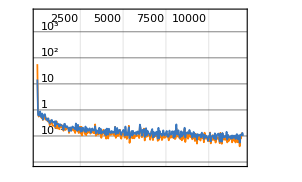
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:7.9min  examples/s:25969
data | ,,  training examples:1020  validation examples:204  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.6×10^-2
validation | ,,  loss:4.83×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

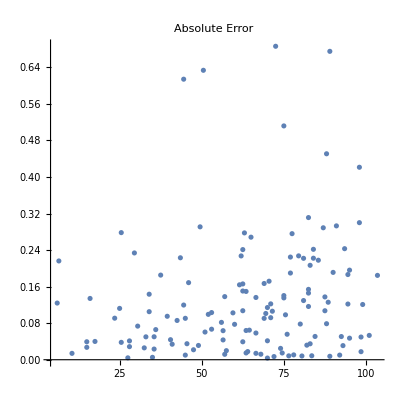

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

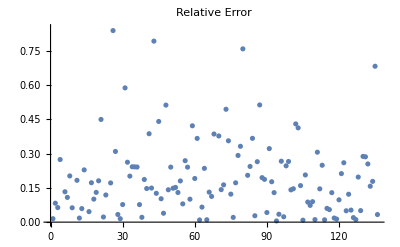

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.257198

#### t3m50q70u80mfpos, Net0, 31 coeffs

```mathematica
t3m50q70u80mfpos=ParallelTable[theta3[m,70,80],{m,50}];
DumpSave["t3m50q70u80mfpos.mx", t3m50q70u80mfpos];
```

```mathematica
<<t3m50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t3m50q70u80mfpos,1];
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
(*t3m50q70u80mfposcsv = Flatten[#, 1] & /@ Transpose[{enc[Keys[data]],N[Values[data]]}];
Export["t3m50q70u80mfpos.csv", t3m50q70u80mfposcsv];*)
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

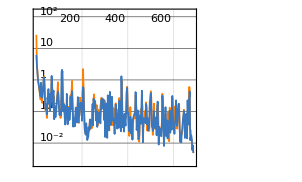
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:15814  rounds:687  time:44s  examples/s:23226
data | ,,  training examples:1470  validation examples:294  processed examples:1012096  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.91×10^-3
validation | ,,  loss:5.41×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

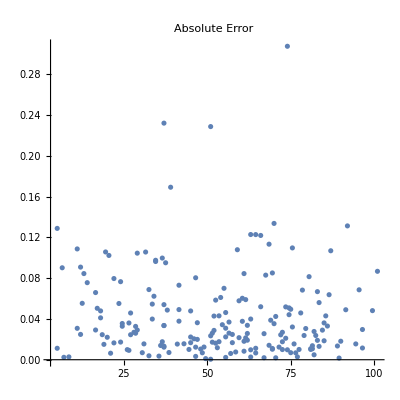

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

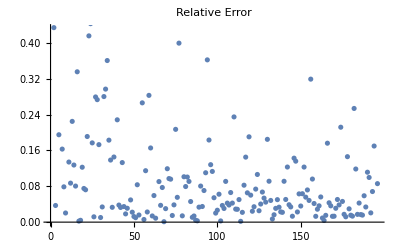

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.129072

```mathematica
(*plist=powersneg[5];*)
plist=klmnneg[5, 400];
```

```mathematica
allprodgenbyΔneg[50,70,plist,plist[[56;;60]],0];
```

```mathematica
rawdata1=Import["jacobibyΔ-klmn-neg2.txt", Path->NotebookDirectory[]];
```